# Wolfram: CodeEquivalenceUtilities

Utilities for testing code equivalence

## Paclet

### Paclet Directory

NotebookDirectory[]

### Manifest

"DefinitionNotebook.nb"H:\Documents\Paclets\CodeEquivalenceUtilities\DefinitionNotebook.nb

"Documentation"

"English"

"Guides"

"CodeEquivalenceUtilities.nb"H:\Documents\Paclets\CodeEquivalenceUtilities\Documentation\English\Guides\CodeEquivalenceUtilities.nb

"ReferencePages"

"Symbols"

"CodeEquivalentQ.nb"H:\Documents\Paclets\CodeEquivalenceUtilities\Documentation\English\ReferencePages\Symbols\CodeEquivalentQ.nb

"EquivalenceTestData.nb"H:\Documents\Paclets\CodeEquivalenceUtilities\Documentation\English\ReferencePages\Symbols\EquivalenceTestData.nb

"FromCanonicalForm.nb"H:\Documents\Paclets\CodeEquivalenceUtilities\Documentation\English\ReferencePages\Symbols\FromCanonicalForm.nb

"MakeCanonicalForm.nb"H:\Documents\Paclets\CodeEquivalenceUtilities\Documentation\English\ReferencePages\Symbols\MakeCanonicalForm.nb

"ToCanonicalForm.nb"H:\Documents\Paclets\CodeEquivalenceUtilities\Documentation\English\ReferencePages\Symbols\ToCanonicalForm.nb

"Tutorials"

"AddingNewTransformationRules.nb"H:\Documents\Paclets\CodeEquivalenceUtilities\Documentation\English\Tutorials\AddingNewTransformationRules.nb

"Kernel"

"CachedValues.wl"H:\Documents\Paclets\CodeEquivalenceUtilities\Kernel\CachedValues.wl

"CanonicalForms"

"Attributes.wl"H:\Documents\Paclets\CodeEquivalenceUtilities\Kernel\CanonicalForms\Attributes.wl

"Common.wl"H:\Documents\Paclets\CodeEquivalenceUtilities\Kernel\CanonicalForms\Common.wl

"ExperimentalRules.wl"H:\Documents\Paclets\CodeEquivalenceUtilities\Kernel\CanonicalForms\ExperimentalRules.wl

"Graphics.wl"H:\Documents\Paclets\CodeEquivalenceUtilities\Kernel\CanonicalForms\Graphics.wl

"Rules.wl"H:\Documents\Paclets\CodeEquivalenceUtilities\Kernel\CanonicalForms\Rules.wl

"Scope.wl"H:\Documents\Paclets\CodeEquivalenceUtilities\Kernel\CanonicalForms\Scope.wl

"Structural.wl"H:\Documents\Paclets\CodeEquivalenceUtilities\Kernel\CanonicalForms\Structural.wl

"CodeEquivalenceUtilities.wl"H:\Documents\Paclets\CodeEquivalenceUtilities\Kernel\CodeEquivalenceUtilities.wl

"Debugging.wl"H:\Documents\Paclets\CodeEquivalenceUtilities\Kernel\Debugging.wl

"EvaluationControl.wl"H:\Documents\Paclets\CodeEquivalenceUtilities\Kernel\EvaluationControl.wl

"Formatting.wl"H:\Documents\Paclets\CodeEquivalenceUtilities\Kernel\Formatting.wl

"init.wl"H:\Documents\Paclets\CodeEquivalenceUtilities\Kernel\init.wl

"SymbolInformation"

"SymbolBlacklist.wl"H:\Documents\Paclets\CodeEquivalenceUtilities\Kernel\SymbolInformation\SymbolBlacklist.wl

"SymbolFlaglist.wl"H:\Documents\Paclets\CodeEquivalenceUtilities\Kernel\SymbolInformation\SymbolFlaglist.wl

"SymbolWhitelist.wl"H:\Documents\Paclets\CodeEquivalenceUtilities\Kernel\SymbolInformation\SymbolWhitelist.wl

"Test.wl"H:\Documents\Paclets\CodeEquivalenceUtilities\Kernel\SymbolInformation\Test.wl

"Types.wl"H:\Documents\Paclets\CodeEquivalenceUtilities\Kernel\Types.wl

"Utilities.wl"H:\Documents\Paclets\CodeEquivalenceUtilities\Kernel\Utilities.wl

"PacletInfo.wl"H:\Documents\Paclets\CodeEquivalenceUtilities\PacletInfo.wl

"Tests"

"CanonicalForms"

"Attributes.wlt"H:\Documents\Paclets\CodeEquivalenceUtilities\Tests\CanonicalForms\Attributes.wlt

"Common.wlt"H:\Documents\Paclets\CodeEquivalenceUtilities\Tests\CanonicalForms\Common.wlt

"Rules.wlt"H:\Documents\Paclets\CodeEquivalenceUtilities\Tests\CanonicalForms\Rules.wlt

"Data"

"EIWLData.wl"H:\Documents\Paclets\CodeEquivalenceUtilities\Tests\Data\EIWLData.wl

"EIWL.wlt"H:\Documents\Paclets\CodeEquivalenceUtilities\Tests\EIWL.wlt

"EvaluationControl.wlt"H:\Documents\Paclets\CodeEquivalenceUtilities\Tests\EvaluationControl.wlt

## Web Content

### Headline Image

```mathematica
graph=Graph[{
a->x,
b->x,
a1->a,
a11->a1,
a12->a1,
a2->a,
a22->a2,
b1->b,
b2->b
},
EdgeStyle->Directive[Thickness[.03],GrayLevel[.85],Arrowheads[.15],Opacity[1]],
VertexSize->Medium,
VertexStyle->Directive[GrayLevel[.85],EdgeForm[None],Opacity[1]],
ImageSize->500,
AspectRatio->1
];
img=Show[HighlightGraph[graph,{Style[PathGraph[FindShortestPath[graph,b2,x],DirectedEdges->True],ColorData[97][1]],Style[PathGraph[FindShortestPath[graph,a22,x],DirectedEdges->True],ColorData[97][2]],
Style[x,ColorData[97][3]]},VertexLabels->{b2->Placed[Framed[Style[Defer@f[…],FontColor->ColorData[97][1],FontSize->36,FontWeight->Bold],Background->White,RoundingRadius->8,FrameMargins->8,FrameStyle->Directive[Thickness[5],ColorData[97][1]]],Center],a22->Placed[Framed[Style[Defer@g[…],FontColor->ColorData[97][2],FontSize->36,FontWeight->Bold],Background->White,RoundingRadius->8,FrameMargins->8,FrameStyle->Directive[Thickness[5],ColorData[97][2]]],Center],
x->Placed[Style["✓",FontWeight->Bold,FontSize->150,FontColor->ColorData[97][3]],{3.5,1.5}]
}],ImageSize->500,AspectRatio->1]/.{HoldPattern[f]->RawBoxes["f"],HoldPattern[g]->RawBoxes["g"],HoldPattern[…]->RawBoxes["…"]};
ImagePad[ImageCrop@Rasterize[img,ImageResolution->144,Background->None],{{0,100},{0,0}},None]
```

-Graphics-

### Basic Description

In a formal language such as type theory, one distinguishes various different notions of equality or equivalence of the terms of the language.

Note that both intensional and extensional type theories may distinguish between intensional and extensional equality (and whether the type theory satisfies function extensionality is yet a separate issue).

Another sort of equality which is very important in type theory is computational, conversional, or reductional equality. This is the congruence on terms generated by various conversion or reduction rules, such as ∞-reduction or ∞-conversion (the choice of rules depends on the type theory).

### Details

Here is a list of distinctions between different notions of equality, in different contexts, where possibly all the following pairs of notions are, in turn, “the same”, just expressed in terms of different terminologies:

the difference between axiomatic and defined equality;
the difference between identity and equality;
the difference between intensional and extensional equality;
the difference between equality judgements and equality propositions,
the difference between equality and isomorphism,
the difference between equality and equivalence,
the possibility of operations that might not preserve equality.

The paradigmatic example of computational equality is a pair of terms like “(λx.x+x)2” and “2+2”, where the second is obtained by β-reduction from the first. In a type theory that includes definitions by recursion, expansion of a recursor is also computational equality. For instance, if addition is defined by recursion, then “2+2” (that is, s(s(0))+s(s(0))) reduces via this rule to “4” (that is, s(s(s(s(0))))).

For better or for worse, however, it is common in type theory to use the phrase “definitional equality” to include computational equality, even though it involves more than mere expansion of definitional abbreviations. There is even a phrase “δ-reduction” for the substitution of definitions regarded as a conversion rule analogous to β-reduction and η-expansion. Thus, even though “2+2” and “4” are not literally equal by definition but only by performing some computation (even if the computation is fairly trivial in this case), the type of equality they do enjoy is generally called definitional.

### Main Guide Page

"Documentation/English/Guides/CodeEquivalenceUtilities.nb"

## Examples

### Initialization for Examples

```mathematica
PacletDirectoryLoad[];
```

```mathematica
Needs[]
```

### Basic Examples

Check if two expressions are equivalent:

```mathematica
CodeEquivalentQ[RandomInteger/@Range[5],Array[RandomInteger,5]]
```

True

View the canonical representations of expressions:

```mathematica
MakeCanonicalForm[RandomInteger/@Range[5]]
```

Table[ℛ[DiscreteUniformDistribution[{0,S1 ∷ Int}]],{S1 ∷ Int,1,5,1}]

```mathematica
MakeCanonicalForm[Array[RandomInteger,5]]
```

Table[ℛ[DiscreteUniformDistribution[{0,S1 ∷ Int}]],{S1 ∷ Int,1,5,1}]

These are directly comparable:

```mathematica
%===%%
```

True

### Scope

Get additional information about the equivalence test:

```mathematica
EquivalenceTestData[
First[Rest[Range/@Range[2^100]]],
Part[Table[Table[j,{j,i}],{i,2^100}],2]
]
```

<|Timing→<|SameQ→0.,ToCanonicalForm1→0.9639954,ToCanonicalForm2→1.519995|>,SameQ→False,CanonicalForms→<|1→HoldComplete[Table[Table[S1 ∷ Int,{S1 ∷ Int,1,S2 ∷ Int,1}],{S2 ∷ Int,1,1267650600228229401496703205376,1}]⟦2⟧],2→HoldComplete[Table[Table[S1 ∷ Int,{S1 ∷ Int,1,S2 ∷ Int,1}],{S2 ∷ Int,1,1267650600228229401496703205376,1}]⟦2⟧]|>,CanonicalEquivalentQ→True,EquivalentQ→True|>

View the sequence of transformations used to convert an expression to its canonical form:

```mathematica
MakeCanonicalForm[Array[RandomInteger,5],"Trace"->True]//Column
```

Array[RandomInteger,5]
Table[RandomInteger[S1],{S1,5}]
Table[RandomInteger[S1],{S1,1,5,1}]
Table[RandomInteger[S1 ∷ Int],{S1 ∷ Int,1,5,1}]
Table[RandomInteger[{0,S1 ∷ Int}],{S1 ∷ Int,1,5,1}]
Table[ℛ[DiscreteUniformDistribution[{0,S1 ∷ Int}]],{S1 ∷ Int,1,5,1}]
Table[ℛ[DiscreteUniformDistribution[{0,S1 ∷ Int}]],{S1 ∷ Int,1,5,1}]

Convert a canonical representation to a normal expression:

```mathematica
MakeCanonicalForm[Array[RandomInteger,5]]
```

Table[ℛ[DiscreteUniformDistribution[{0,S1 ∷ Int}]],{S1 ∷ Int,1,5,1}]

```mathematica
FromCanonicalForm[%]
```

Table[RandomVariate[DiscreteUniformDistribution[{0,S1}]],{S1,1,5,1}]

Evaluate:

```mathematica
ReleaseHold[%]
```

{1,1,1,0,1}

### Neat Examples

Here is a list of expressions, some of which are equivalent to others:

```mathematica
expressions={
HoldForm[Table[i,{i,5},{j,i+2}]],
HoldForm[Array[Range,5,3]],
HoldForm[Table[ConstantArray[i,i+2],{i,5}]],
HoldForm[First[Rest[Range/@Range[10]]]],
HoldForm[Range/@Range[3,7]],
HoldForm[Part[Table[Table[j,{j,i}],{i,10}],2]]
};
```

Find the sequence of transformations for each expression:

```mathematica
Short[traces=Most@ToCanonicalForm[#,"Trace"->True]&/@expressions]
```

{{Table[i,{i,5},{j,i+2}],«5»,Table[Table[S1 ∷ Int,{S2 ∷ Int,1,2+S1 ∷ Int,1}],{S1 ∷ Int,1,5,1}]},{«1»},«2»,{Range/@Range[3,7],«10»},{«1»}}

Generate a graph for each sequence:

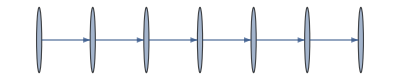
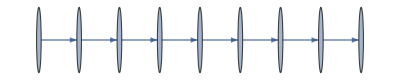
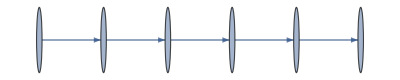
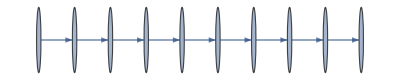
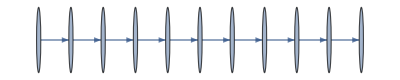
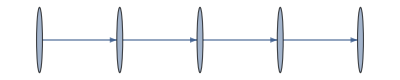

```mathematica
paths=Graph[DirectedEdge@@@Partition[#,2,1]]&/@traces
```

Combine the graphs:

```mathematica
graph=Graph[GraphUnion@@paths,];
```

Equivalent expressions converge to the same connected component:

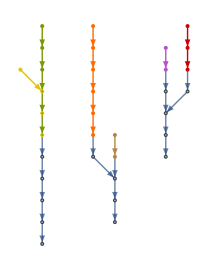

```mathematica
HighlightGraph[graph,paths]
```

Group the expressions into their corresponding equivalence class:

```mathematica
grouped=GroupBy[expressions,ToCanonicalForm]
```

<|Table[Table[S1 ∷ Int,{S2 ∷ Int,1,2+S1 ∷ Int,1}],{S1 ∷ Int,1,5,1}]→{Table[i,{i,5},{j,i+2}],Table[ConstantArray[i,i+2],{i,5}]},Table[Table[S1 ∷ Int,{S1 ∷ Int,1,2+S2 ∷ Int,1}],{S2 ∷ Int,1,5,1}]→{Array[Range,5,3],Range/@Range[3,7]},Table[Table[S1 ∷ Int,{S1 ∷ Int,1,S2 ∷ Int,1}],{S2 ∷ Int,1,10,1}]⟦2⟧→{First[Rest[Range/@Range[10]]],Table[Table[j,{j,i}],{i,10}]⟦2⟧}|>

```mathematica
TableForm[KeyValueMap[Reverse@*List,grouped]]
```

Table[i,{i,5},{j,i+2}]
Table[ConstantArray[i,i+2],{i,5}] | Table[Table[S1 ∷ Int,{S2 ∷ Int,1,2+S1 ∷ Int,1}],{S1 ∷ Int,1,5,1}]
Array[Range,5,3]
Range/@Range[3,7] | Table[Table[S1 ∷ Int,{S1 ∷ Int,1,2+S2 ∷ Int,1}],{S2 ∷ Int,1,5,1}]
First[Rest[Range/@Range[10]]]
Table[Table[j,{j,i}],{i,10}]⟦2⟧ | Table[Table[S1 ∷ Int,{S1 ∷ Int,1,S2 ∷ Int,1}],{S2 ∷ Int,1,10,1}]⟦2⟧

## Source & Additional Information

### Creator

Richard Hennigan <richardh@wolfram.com>

### Source Control Repository

https://github.com/UserName/MyPaclet

### Keywords

code equivalence

code transformations

equivalent input

same code

canonical

transform code

### Categories

Cloud & Deployment |  Core Language & Structure
 Data Manipulation & Analysis |  Engineering Data & Computation
 External Interfaces & Connections |  Financial Data & Computation
 Geographic Data & Computation |  Geometry
 Graphs & Networks |  Higher Mathematical Computation
 Images |  Knowledge Representation & Natural Language
 Machine Learning |  Notebook Documents & Presentation
 Scientific and Medical Data & Computation |  Social, Cultural & Linguistic Data
 Sound & Video |  Strings & Text
 Symbolic & Numeric Computation |  System Operation & Setup
 Time-Related Computation |  User Interface Construction
 Visualization & Graphics |

### Related Resource Objects

SameExpressionShapeQ

SameInstanceQ

SameAsQ

CheckMatch

DefinitionData

EvaluationTiming

ExpressionLineDiff

ReplaceContext

### Source/Reference Citation

Source, reference or citation information

### Links

Starting Out: Elementary Arithmetic: Elementary Introduction to the Wolfram Language

### Compatibility

#### Wolfram Language Version

12.3+

#### Operating System

Windows |  Mac |  Unix

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

#### Environments

SessionLocal or cloud interactive session |  ScriptScript run in batch mode |  SubkernelParallel or grid subkernel
 WebEvaluationCloud evaluation initiated by an HTTP request |  WebAPIAPI called through an HTTP request |  ScheduledScheduled task
 BatchJobRemote batch job |  |

#### Cloud Support

Supported in cloud

## Author Notes

Additional information about limitations, issues, etc.